```mathematica
Clear["Global'*"]
```

Σταθερές (Constants)

```mathematica
MSun=1.989*^30;
h=6.62607015*10^(-34);
hev=4.135667696*10^(-15);
hbarev=6.5821×10^(-16);
hbar=1.054571817*10^(−34);
G=6.6743*10^(-11);
kev=8.617333262*10^(-5);
c=299792458;
mn=939565413.3;
mnkg=1.67492749804*10^(-27);
```

Αριθμητική Πυκνότητα Αστέρων Νετρονίων (Neutron star numerical density)

```mathematica
RNS=10600; (*Radius on NS in meters*)
VNS=4/3*Pi*RNS^3//N (*Volume of NS in m^3*)
ρNS=1.4*MSun/VNS (*The mass density of a NS with mass 1.4MSun in kg/m^3*)
n=ρNS/mnkg(*The numerical density of the NS in m^(-3)*)
```

4.98892×10^12

5.58157×10^17

3.33243×10^44

Ανάλυση Fermi (Fermi Analysis)

```mathematica
a=(3*Pi^2*n)^(2/3);
b=hbar^2/(2*mnkg);
Ef=a*b;(*The Fermi energy of the neutrons in Joule*)
pf=hbarev*(3*Pi^2*n)^(1/3);(*The fermi momentum of neutrons in ev/c*)
pfev=pf*c(*The fermi momentum of neutrons in ev*)
pfGev=pfev/(10^9) (*The fermi momentum of neutrons in GeV*)
γ=γ/.Solve[Ef+mnkg*c^2==γ*mnkg*c^2,γ][[1]](*The calculation of Lorentz constant γ for the fastest neutrons*)
β=β/.Solve[γ==1/Sqrt[1-β^2],β][[2]](*The calculation of Lorentz constant β for the fastest neutrons*)
uf=c*β (*The fermi speed of the neutrons in m/s*)
f[u]=3*u^2/uf^3; (*The Fermi distribution*)
AverageUf=Integrate[u*f[u],{u,0,uf}]/(c*Integrate[f[u],{u,0,uf}])(*The calculation of the average speed of the neutrons*)
```

4.23233×10^8

0.423233

1.10146

0.41921

1.25676×10^8

0.314407

Bondi -Hoyle προσαύξηση (Bondi-Hoyle accretion model)

```mathematica
cslower=2*10^8;(*The lowest approx. of the sound-speed in m/s*)
(cslower/c)^2 //N (*The lowest approx. of the sound -speed as a percentage of the speed of light c*)
cshigher=1.5*10^8 ;(*The highest approx. of the sound-speed in m/s*)
(cshigher/c)^2 //N(*The highest approx. of the sound-speed as a percentage of the speed of light c*)
cs=(cshigher+cslower)/2; (*The speed of sound approx. we use in m/s*)
(cs/c)^2 (*The speed of sound approx. we use as a percentage of the speed of light c*)
λs53=Limit[(1/2)^(((g+1))/(2*(g-1)))*((5-3*g)/4)^-((5-3*g)/(2*g-1)),g->5/3](* The eigenvalue when the polytropic exponent g=5/3*)
```

0.44506

0.250346

0.340749

1/4

9.93513×10^-28 M^2

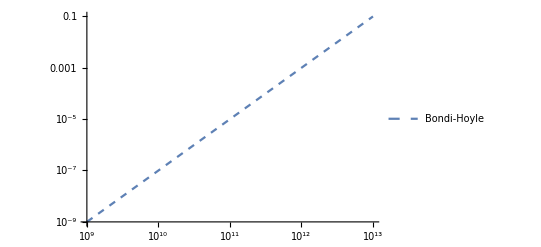

```mathematica
BH[u]:=f[u]*4*Pi*λs53*G^2*M^2*mnkg*n/(((cs)^2+u^2)^(3/2));(*The integrated function in the calculation of the Bondi-Hoyle accretion rate*)
Bondi[M_]=Integrate[BH[u], {u, 0, uf}](*The accretion rate of the Bondi-Hoyle model in kg/sec and M is the black hole mass in kg*)
PlotBondi=LogLogPlot[Bondi[M],{M,10^9,10^13},PlotStyle->Dashed,PlotLegends->{"Bondi-Hoyle"}](*The plot of the accretion rate of the Bondi-Hoyle model in kg/sec in turms of M in kg*)
```

Unruh προσαύξηση (Unruh accretion model)

```mathematica
ks[u]=((2*Pi*G*M*mnkg)/(h*c) )*(1+u^2)/(u*Sqrt[1-u^2]);(*The variable ξ in turms of u, whitch is the speed of the neutrons/c*)
Series[x/(1-Exp[-x]),{x,0,1}](*The Taylor series of f(ξ)*)
s[u_]:=(1+ks[u]/2)2*Pi*G^2*M^2/(u)(*The Unruh cross section after we subsitute the Taylor series of f(ξ)*)
```

1+x/2+O[x]^2

```mathematica
umax=uf/c (*The fermi speed of the neutrons as a percentage of the speed of light c*)
```

0.41921

(5.7981×10^-28+4.1883×10^-39 M) M^2

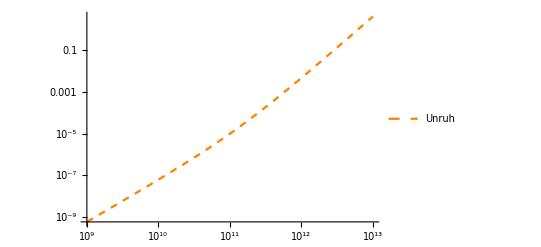

```mathematica
Unruh[M_]=Integrate[mnkg*n*u(3 *u^2/uf^3)*s[u],{u,0,umax}](*The accretion rate of the Unhur model in kg/sec and M is th black hole mass in kg*)
PlotUnruh=LogLogPlot[Unruh[M],{M,10^9,10^13},PlotStyle->{Orange,Dashed },PlotLegends->{"Unruh"}] (*The plot of the accretion rate of the Unruh model in kg/sec in turms of M in kg*)
```

Ακτινοβολία Hawking (Hawking Radiation rate)

```mathematica
Cμ=4.53*10^11;
Cud=1.6*10^11;
Cs=9.6*10^10;
Cg=1.1*10^11;
Ctaf=2.68*10^10; (*The constants needed for the definition of f(M) of the Hawking mechanism in kg*)
Cc=1.56*10^10;
Cb=9.07*10^9;
Ct=0.48*10^9;
Cπ0=2.08*10^11;
Cπ=2.01*10^11;

f[M_]:=1.569+0.569*(Exp[-M/Cμ]+3Exp[-M/Cud]+3Exp[-M/Cud]+3Exp[-M/Cs]+3Exp[-M/Cc]+Exp[-M/Ctaf]+3Exp[-M/Cb]+3Exp[-M/Ct])+0.963*Exp[-M/Cg]
```

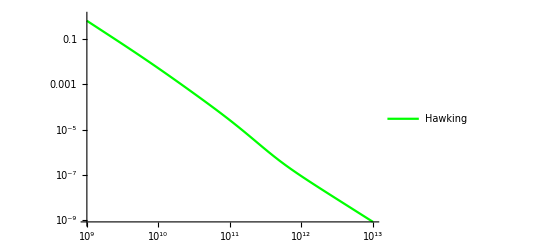

```mathematica
Hawking[M_]:=-5.34*10^(16)f[M]/(M^2) (*The mass loss rate of the Hawking radiation model in kg/sec and M is th black hole mass in kg*)
PlotHawking=LogLogPlot[Abs[Hawking[M]],{M,10^9,10^13},PlotStyle->Green,PlotLegends->{"Hawking"}] (*The plot of the absolute value of the mass rate of the Hawking radiation model in kg/sec in turms of M in kg*)
```

### Όρια Μοντέλων (Limits of models)

#### 1)Bondi - Hoyle

```mathematica
Rschw=2G*M/c^2 (*The Schwarzschild radius of the black hole in meters*)
pfsi=hbar*(3*Pi^2*n)^(1/3); (* The fermi momentum of the neutrons in SI units*)
k=pfsi/hbar (*The wavenumber of particles with momentum = pfsi in m^(-1)*)
```

1.48523×10^-27 M

2.14483×10^15

```mathematica
ann=-18.5*10^(-15) (*The scattering length of the neutron-neutron interaction in meters*)
rnn=2.75*10^(-15) (*The effective range of the neutron-neutron interaction in meters*)
```

-1.85×10^-14

2.75×10^-15

```mathematica
σ=σ/.Solve[σ/(4*Pi)==1/(k^2+ann^2-k^2ann*rnn+1/4*k^2*rnn),σ][[1]](*The corresponding cross section of the neutron-neutron interaction in the NS in m^2*)
```

2.73163×10^-30

```mathematica
λmfp=1/(n*σ) (*The mean free path of the neutrons in meters*)
```

1.09854×10^-15

```mathematica
Reduce[c^2Rschw/(cs^2)>λmfp](*The necessary criteria for the Bondi-Hoyle model to hold*)
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

M>2.52033×10^11

#### 2) Unruh

```mathematica
Reduce[c^2Rschw/(cs^2)<λmfp] (*The 1st necessary criteria for the Unhur model to hold*)
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

M<2.52033×10^11

```mathematica
mnnew=1.33699702196*10^(-27) (* The mass m^*_N of neutrons due to the nuclear powers inside the NS in kg*)
```

1.337×10^-27

```mathematica
ldb=h/(mnnew*c*AverageUf) (*The De Broglie wavelength of the neutrons in meters*)
```

5.2579×10^-15

```mathematica
Reduce[M<ldb c^2/(2G)] (*The 2nd necessary criteria for the Unhur model to hold*)
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

M<3.54012×10^12

```mathematica
Mlimit=2.5203313818943997*^11 (*The final Mlimit value according to the previous analysis.*)
```

2.52033×10^11

### Υπολογισμός του Mcrit (Computation of Mcrit)

```mathematica
FindRoot[Abs[Hawking[M]]==Bondi[M],{M,10^11}](*The 1st try of computing Mcrit. The result is lower than Mlimit so it's rejected*)
```

{M→1.2377×10^11}

```mathematica
FindRoot[Abs[Hawking[M]]==Unruh[M],{M,1.1*10^11,1.2*10^11}](*The 2nd try of computing Mcrit. The result is lower than Mlimit so it's accepted*)
```

{M→1.21315×10^11}

```mathematica
Mcrit= 1.2131461216592548*^11(*The result we get after the second try of computing MCrit in kg*)
```

1.21315×10^11

```mathematica
Abs[Hawking[Mcrit]]-Unruh[Mcrit](*The presision of our 2nd try of computing MCrit*)
```

1.11808×10^-19

### Συνολική Γραφική (Overall Plot)

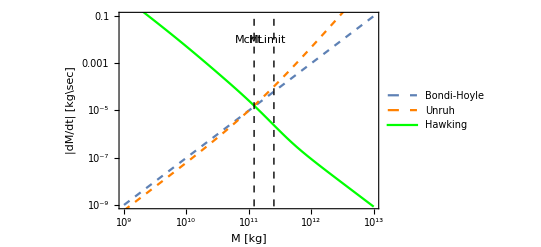

```mathematica
Show[PlotBondi,PlotUnruh,PlotHawking,Frame->True, FrameLabel->{"M [kg]","|dM/dt| [kg\sec]"},FrameStyle->Directive[Black,Thick,14], LabelStyle->{TextAlignment->Center,BaselinePosition->Bottom},Epilog->{Thin,Dashed,InfiniteLine[{{Log@Mlimit,0},{Log@Mlimit,1}}],InfiniteLine[{{Log@Mcrit,0},{Log@Mcrit,1}}],First@Graphics[Rotate[ Text["MLimit",{Log@(2*10^11),Log@(10^(-2))}],90 Degree]],First@Graphics[Rotate[Text["Mcrit",{Log@(10^11),Log@(10^(-2))}],90 Degree]]}] (*The overall plot that includes the Bondi-Hoyle and Unhur accretion rates, the Hawking mass loss rate in kg/sec and the values of MLimit and Mcrit all as a fuction of the black hole mass M in kg*)
```

### Υπολογισμος του χρόνου εξάτμησης Μελανής Οπής τevap (Computation of the evaporation time of Βlack Hole τevap): M<MCrit

```mathematica
g[M_]:=1/(Hawking[M]) (* The integrated function in the calculation of τevap *)
```

```mathematica
numPoints=1000;(*List containing the number of points where we will calculate τevap *)
MLower=10^9;(*The minimum black hole mass where this Hawking radiation model can be used*)
```

```mathematica
MValues=Range[MLower,Mcrit,(Mcrit-MLower)/(numPoints-1)];(*List containing equally spaced points from 10^9 to MCrit. There's numpoints of them*)
```

```mathematica
integralResults=NIntegrate[g[#],{M,#,MLower}]&/@MValues; (*The numerical solution of the integral that gives us τevamp at every point of MValues*)
```

```mathematica
selectedData=Transpose[{MValues,integralResults}][[1;;1000]];(*The value of τevap gets corrisponded to the appropriate Mass or Mvalue*)
```

```mathematica
fit=NonlinearModelFit[selectedData,A M^3,{A},M](*The appropriate fit for our data that gives us τevamp as a function of the black hole mass M*)
```

FittedModel[3.92968×10^-18 M^3]

```mathematica
Show[ListPlot[selectedData,Frame->True,FrameLabel->{"M [kg]","tevamp [sec]"},FrameStyle->Directive[Black,Thick,10],PlotLabel->"Υπολογισμός του χρόνου εξάτμισης"],Plot[fit[M],{M,10^9,Mcrit},PlotStyle->{Red,Dashed}]](*The numerical values of τevap ploted at the corresponding mass and our fit of the data*)
```

-Graphics-

### Υπολογισμός του χρόνου απορρόφησης του αστέρα νετρονίων (Computation of the neutron star’s absorption time) τabsorb

#### 1) MCrit<M<MLimit

```mathematica
gU[M_]:=1/(4.1883009797106704*^-39*M^3) (*The integrated function in the calculation of τabsorb when MCrit<M<MLimit (Unhur dominates)*)
```

```mathematica
Myr=365*24*60*60*10^6; (*Number of seconds in 1 million years*)
```

```mathematica
τU=Integrate[gU[M],{M,M,MLimit}] (*τabsorb when MCrit<M<MLimit in sec, as a function of the black hole mass in kg*)
```

ConditionalExpression[2.3876×10^38 (1/(2 M^2)-1/(2 MLimit^2)),(M/(M-MLimit)≠0&&Re[M/(-M+MLimit)]≥0)||Re[M/(M-MLimit)]>1||M/(M-MLimit)∉ℝ]

```mathematica
τU/(Myr*Mlimit^2) (* τabsorb when MCrit<M<MLimit in Myrs as a function of the black hole mass in MLimit*)
```

ConditionalExpression[119.19 (1/(2 M^2)-1/(2 MLimit^2)),(M/(M-MLimit)≠0&&Re[M/(-M+MLimit)]≥0)||Re[M/(M-MLimit)]>1||M/(M-MLimit)∉ℝ]

```mathematica
1/(2Mlimit^2) (*The value of 1/(2Mlimit^2), a term we can see in the final result for τu*)
```

7.87145×10^-24

#### 2) M>MLimit

```mathematica
gBH[M_]:=1/(Bondi[M])(*The integrated function in the calculation of τabsorb when M>MLimit (Bondi-Hoyle dominates)*)
```

```mathematica
τΒΗ=Integrate[gBH[M],{M,M,MNS}] (*τabsorb when M>MLimit is sec as a function of the black hole mass in kg*)
```

ConditionalExpression[1.00653×10^27 (1/M-1/MNS),(M/(M-MNS)≠0&&Re[M/(-M+MNS)]≥0)||Re[M/(M-MNS)]>1||M/(M-MNS)∉ℝ]

```mathematica
τΒΗ/(Myr*Mlimit)(* τabsorb when M>MLimit in Myrs as a function of the black hole mass in MLimit*)
```

ConditionalExpression[126.637 (1/M-1/MNS),(M/(M-MNS)≠0&&Re[M/(-M+MNS)]≥0)||Re[M/(M-MNS)]>1||M/(M-MNS)∉ℝ]

```mathematica
1/(1.4MSun) (*The value of 1/(1.4MSun), a term we can see in the final result for τBH*)
```

3.59118×10^-31